Error analysis (§3.5):

```mathematica
Quit[]
```

```mathematica
r={0.6,0.8,1.0,1.2,1.4}
```

{0.6,0.8,1.,1.2,1.4}

```mathematica
meanR=(1/5)*Total[r]
varR=(1/5)*Total[(r-meanR)^2]
stdR=Sqrt[varR]
```

1.

0.08

0.282843

```mathematica
r
Mean[r]
Variance[r]
StandardDeviation[r]
```

{0.6,0.8,1.,1.2,1.4}

1.

0.1

0.316228

Note the difference between the above results for the variance. Remember that Mathematica calculates the sample variance s^2 which is corrected for the fact that in practice only part of a population will be measured by reducing the degrees of freedom n by one: Variance[list] is equivalent to Total[(list-Mean[list])^2]/(Length[list]-1). In the first calculation, we calculated the population variance σ^2 using n instaed of n-1.

```mathematica
Clear[v]
v[r_]:=(4/3)*Pi*r^3
```

```mathematica
vol=v[r]
meanV=(1/5)*Total[vol]
varV=(1/5)*Total[(vol-meanV)^2]
stdV=Sqrt[varV]
```

{0.904779,2.14466,4.18879,7.23823,11.494}

5.1941

14.5151

3.80987

```mathematica
v[meanR]
```

4.18879

```mathematica
meanR=1.0
stdR=0.28
dV=v'[meanR]
ddV=v''[meanR]
```

1.

0.28

12.5664

25.1327

```mathematica
meanVest=v[meanR]+0.5*v''[meanR]*stdR^2
stdVest=v'[meanR]*stdR
```

5.17399

3.51858

```mathematica
meanR=(1/5)*Total[r]
varR=(1/5)*Total[(r-meanR)^2]
stdR=Sqrt[varR]
```

1.

0.08

0.282843

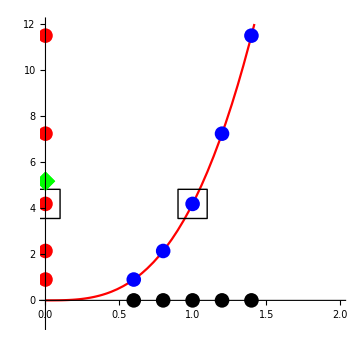

```mathematica
lr={{r[[1]],0},{r[[2]],0},{r[[3]],0},{r[[4]],0},{r[[5]],0}};
lV={{0,vol[[1]]},{0,vol[[2]]},{0,vol[[3]]},{0,vol[[4]]},{0,vol[[5]]}};
lrV= {{r[[1]],vol[[1]]},{r[[2]],vol[[2]]},{r[[3]],vol[[3]]},{r[[4]],vol[[4]]},{r[[5]],vol[[5]]}};
plot1=Plot[v[r],{r,0,2},PlotRange->{-1,12},PlotStyle->Red];
plot2=ListPlot[lr,PlotMarkers->{"●",15},PlotStyle->Black];
plot3=ListPlot[lrV,PlotMarkers->{"●",15},PlotStyle->Blue];
plot4=ListPlot[lV,PlotMarkers->{"●",15},PlotStyle->Red];
plot5=ListPlot[{{meanR,v[meanR]},{0,v[meanR]}},PlotMarkers->{"□",30},PlotStyle->Black];
plot6=ListPlot[{{0,meanVest}},PlotMarkers->{"◆",20},PlotStyle->Green];
Show[plot1,plot2,plot3,plot4,plot5,plot6,AspectRatio->1/1,ImageSize->Medium]
```